#### (06.05.2021) Графики 3D-модели

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb

```mathematica
data=Import["C:\\Users\\user\\Documents\\Wolfram Mathematica\\Проект\\Расчёты .nb\\results3D_40_50.txt","table"];
```

```mathematica
i:=1;
Do[Print[i, " - ",n];i++;,{n,data[[1]]}]
```

1 - N

2 - J

3 - h

4 - mean_R_sq

5 - err_mean_R_sq

6 - mean_R_gyr_sq

7 - err_mean_R_gyr_sq

8 - mean_e

9 - err_mean_e

10 - mean_e_sq

11 - err_mean_e_sq

12 - mean_e_fourth

13 - err_mean_e_fourth

14 - mean_m

15 - err_mean_m

16 - mean_m_sq

17 - err_mean_m_sq

18 - mean_m_fourth

19 - err_mean_m_fourth

```mathematica
Needs["ErrorBarPlots`"]
Ls={100,300};
```

График квадрата намагниченности

```mathematica
plot1={};
Do[
AppendTo[plot1,Map[{{#[[2]],#[[16]]},ErrorBar[#[[17]]]}&,Select[data,#[[1]]==n&]]];
,{n,Ls}];
```

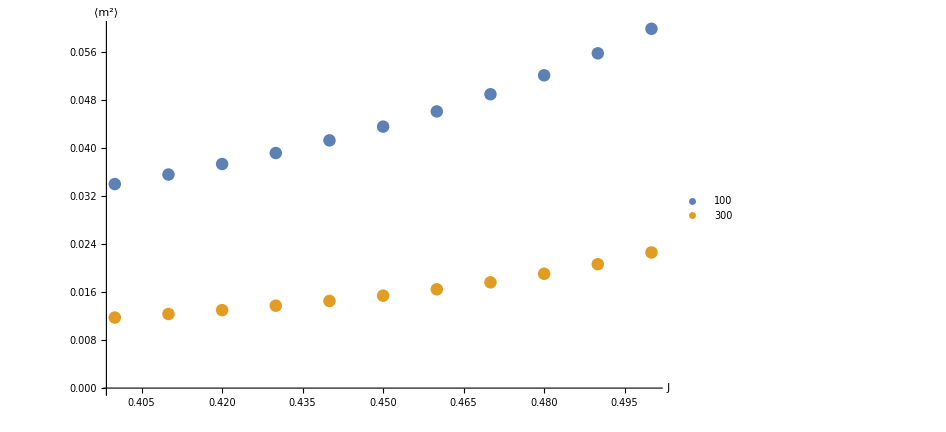

```mathematica
ErrorListPlot[plot1,PlotLegends->Ls,AxesLabel->{Style["J",15],Style["⟨m^2⟩",15]},ImageSize->700]
```

```mathematica
ErrorOfU4[data0_]:=Module[{lData=data0,dM2={},dM4={},dU4={}},
Needs["ErrorBarPlots`"];
dM2 = RandomVariate[NormalDistribution[lData[[16]], lData[[17]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[18]], lData[[19]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
Return[StandardDeviation[HistogramDistribution[dU4]]]];
```

График кумулянта Биндера

```mathematica
plot2={};
Do[
AppendTo[plot2,Map[{{#[[2]],1-(#[[18]])/(3*(#[[16]])^2)},ErrorBar[ErrorOfU4[#]]}&,Select[data,#[[1]]==n&]]];
,{n,Ls}];
```

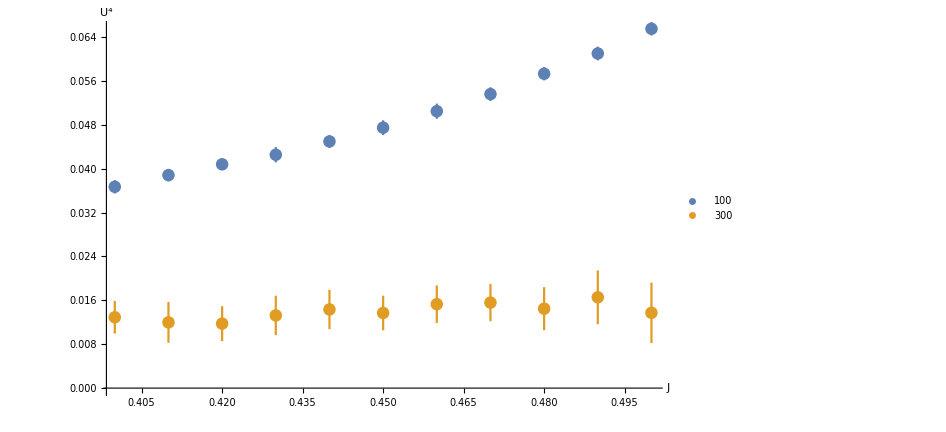

```mathematica
ErrorListPlot[plot2,PlotLegends->Ls,AxesLabel->{Style["J",16],Style["U^4",16]},ImageSize->700]
```

График квадрата энергии

```mathematica
plot3={};
Do[
AppendTo[plot3,Map[{{#[[2]],#[[10]]},ErrorBar[#[[11]]]}&,Select[data,#[[1]]==n&]]];
,{n,Ls}];
```

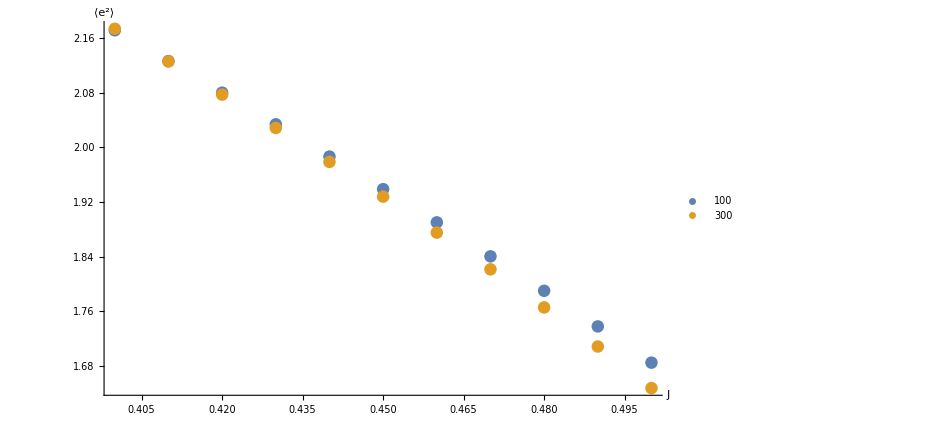

```mathematica
ErrorListPlot[plot3,PlotLegends->Ls,AxesLabel->{Style["J",16],Style["⟨e^2⟩",16]},ImageSize->700]
```

### (10.05.2021) Новые данные (50-60)

```mathematica
data=Import["C:\\Users\\user\\Documents\\Wolfram Mathematica\\Проект\\Расчёты .nb\\results3D_50_60.txt","table"];
```

```mathematica
Needs["ErrorBarPlots`"]
Ls={100,300};
```

График квадрата намагниченности

```mathematica
plot1={};
Do[
AppendTo[plot1,Map[{{#[[2]],#[[16]]},ErrorBar[#[[17]]]}&,Select[data,#[[1]]==n&]]];
,{n,Ls}];
```

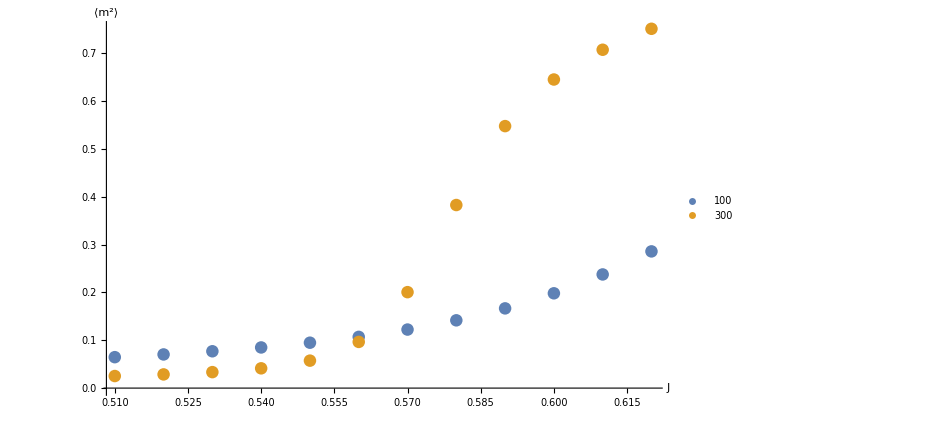

```mathematica
ErrorListPlot[plot1,PlotLegends->Ls,AxesLabel->{Style["J",15],Style["⟨m^2⟩",15]},ImageSize->700]
```

```mathematica
ErrorOfU4[data0_]:=Module[{lData=data0,dM2={},dM4={},dU4={}},
Needs["ErrorBarPlots`"];
dM2 = RandomVariate[NormalDistribution[lData[[16]], lData[[17]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[18]], lData[[19]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
Return[StandardDeviation[HistogramDistribution[dU4]]]];
```

График кумулянта Биндера

```mathematica
plot2={};
Do[
AppendTo[plot2,Map[{{#[[2]],1-(#[[18]])/(3*(#[[16]])^2)},ErrorBar[ErrorOfU4[#]]}&,Select[data,#[[1]]==n&]]];
,{n,Ls}];
```

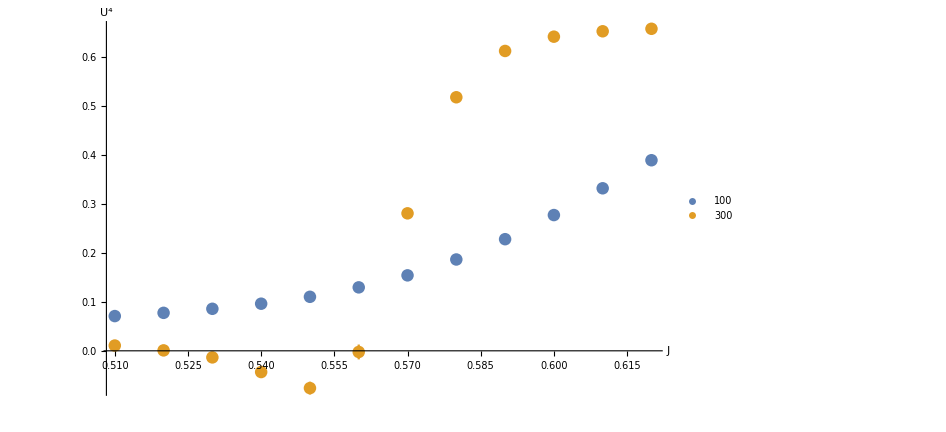

```mathematica
ErrorListPlot[plot2,PlotLegends->Ls,AxesLabel->{Style["J",16],Style["U^4",16]},ImageSize->700]
```

График квадрата энергии

```mathematica
plot3={};
Do[
AppendTo[plot3,Map[{{#[[2]],#[[10]]},ErrorBar[#[[11]]]}&,Select[data,#[[1]]==n&]]];
,{n,Ls}];
```

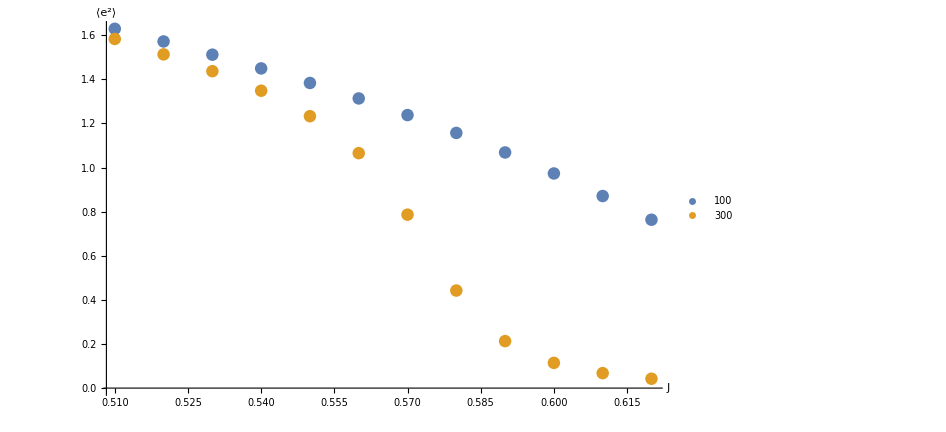

```mathematica
ErrorListPlot[plot3,PlotLegends->Ls,AxesLabel->{Style["J",16],Style["⟨e^2⟩",16]},ImageSize->700]
```